# HYMNS.nb The HYMNs for GR(2,2) and GR(4,4) as in arXiv:XXXX.XXXXX [hep-th] Complete Check of GR(2,2), random check of GR(4,4)

```mathematica
$RecursionLimit=Infinity
```

∞

## Import the Adinkra package

```mathematica
<<Adinkra`
```

```mathematica
BuildDate[Adinkra]
```

190304

### Function Lists

```mathematica
FunctionList[Adinkra]
```

SpaceTime:
IndexRange[SpaceTime][Index], Index = mu, a, or RaiseCode

coordinates, Ϛ[mu], η[mu,nu], Cmetric[[a,b]], InverseCmetric[[a,b]], UD[Field,Ϛ[mu]] , Lap[Field], UP, DOWN, RaiseSTIndex[Field,RaiseCode1,RaiseCode2,...,RaiseCoden], RaiseFermionIndex[Field]

****************************************************************************************
****************************************************************************************

GenerateLandR:
NColors[D,Phi,Psi], LTable[DColor,Phi,Psi], RTable[DColor,Phi,Psi],GenerateLandR[DColor,Phi,Psi,Rep]

****************************************************************************************
****************************************************************************************

AdinkraEssentials:
IndexRange[AdinkraEssentials][Index], Index = p1, II, ReportLevel, or pm

***IMPORTANT****: Default Settings are VScaleFactor = VtildeScaleFactor = -I, VsoNScaleFactor = -I/(2 VsoNScaleFactor), VtildesoNScaleFactor = -I/(2 VtildesoNScaleFactor)

Reports: AdinkraReport[Rep,ReportLevel], AdinkraPreliminaryReport[L,R], AdinkraPreliminaryReport[Rep], AdinkraPreliminaryReportO[Rep], AdinkraHoloMonoReport[Rep], AdinkraSummaryReport[Rep], AdinkraFullReport[Rep]

Basic Functions: nMatrices[Matrices], nRows[Matrices], nColumns[Matrices], Commute[Matrix1,Matrix2], NColors[Rep], NColors[L,R], dmin[N], dbosons[Rep], dbosons[L,R], dfermions[Rep], dfermions[L,R], WordW[{p1,p2,...,pN}]

Intense Calculations: Gadget[Rep1,Rep2], BosonGadget[Rep1,Rep2], ListOfIdenticalMonoOrHolo[MonoOrHolo,Rep], NumDistinctHoloOrMono[HoloOrMono,Rep]

Print Functions: PrintL[Rep][II], PrintR[Rep][II], PrintGALR[Rep][II,JJ], PrintGARL[Rep][II,JJ], PrintV[Rep][II,JJ], PrintVtilde[Rep][II,JJ], PrintZetaGen[Rep][II], PrintHoloraumy[Rep][{p1,p2,...,pN}], PrintMonodromy[Rep][{p1,p2,...,pN}],PrintZetatildeGen[Rep][II], PrintHoloraumytilde[Rep][{p1,p2,...,pN}], PrintMonodromytilde[Rep][{p1,p2,...,pN}], PrintVtildePM[pm][Rep][II,JJ], PrintVtildePM[pm][Rep][II,JJ], PrintAllL[Rep], PrintAllR[Rep], PrintAllGALR[Rep], PrintAllGARL[Rep], PrintAllV[Rep], PrintAllVtilde[Rep], PrintAllZetaGen[Rep], PrintAllHoloraumy[Rep], PrintAllMonodromy[Rep],PrintAllZetatildeGen[Rep], PrintAllHoloraumytilde[Rep], PrintAllMonodromytilde[Rep], PrintAllVtildePM[pm][Rep], PrintAllVtildePM[pm][Rep], ,PrintSigmaProduct[Matrix], PrintLSigmaProduct[Rep], PrintRSigmaProduct[Rep]

Test Functions: CorrectDimensions[Rep], CorrectDimensions[L,R], TransposeTest[Rep], TransposeTest[L,R], InverseTest[Rep], InverseTest[L,R], RO[Rep], Chi0Report[L,R], GATest[Rep], GATest[L,R], soNTest[Matrices], su2Test[MgenPM[pm]][Rep], MutuallyCommuteTest[M1,M2], LinearlyIndependent[Mgen]

Data generated by GenerateAdinkraData[Rep], GenerateAdinkraData[Rep,Orthogonal], GenerateAdinkraDataO[Rep], GenerateAdinkraData[Rep,L], or GenerateAdinkraData[Rep,L,R]:
L[Rep], R[Rep], GALR[Rep], GARL[Rep], chi0[Rep], ncis[Rep], ntrans[Rep], V[Rep], Vtilde[Rep], VsoN[Rep], VtildesoN[Rep], ZetaGen[Rep], Holoraumy[Rep], Monodromy[Rep], ZetatildeGen[Rep], Holoraumytilde[Rep], Monodromytilde[Rep], VPM[pm][Rep], VtildePM[pm][Rep], VsoNPM[pm][Rep], VtildesoNPM[pm][Rep] cSoln[V[Rep]], cSoln[Vtilde[Rep]]

****************************************************************************************
****************************************************************************************

BasisDecomposition:
IndexRange[BasisDecomposition][Index], Index = mu, ahat, a, d, or n

General Matrix Tools:
sigma[mu], αmatrix[ahat], βmatrix[ahat], SigmaProduct[mu1,mu2,...,mun], SigmaProductMF[mu1,mu2,...,mun], SigmaMatrixProduct[mu,AnyMatrix], ρmatrix[mu,nu], ωmatrix[n][a], Basis[d][a,mu,nu], TestOrthogonalσ, TestρOrthogonal, TestωOrthogonal[n], TestBasisOrthogonal[d], Coeffs[d][Matrix][a,mu,nu]

GenerateCoeffs[Rep] generates adinkra representation specific functions:
LCoeffs[Rep][II], CheckLCoeffs[Rep], RCoeffs[Rep][II], CheckRCoeffs[Rep], VCoeffs[Rep][II,JJ], CheckVCoeffs[Rep], VtildeCoeffs[Rep][II,JJ], CheckVtildeCoeffs[Rep], VPMCoeffs[pm][Rep][II,JJ], CheckVPMCoeffs[pm][Rep], VtildePMCoeffs[pm][Rep][II,JJ], CheckVtildePMCoeffs[pm][Rep], NumberNonZero[LCoeffsMat], CoeffsSummaryReport[Rep], CoeffsFullReport[Rep], CMessage[Rep][mi,si]

Print Functions:
 PrintSigmaProduct[Matrix], PrintBasis[Matrix], PrintLBasis[Rep][II], PrintRBasis[Rep][II], PrintGALRBasis[Rep][II,JJ], PrintGARLBasis[Rep][II,JJ], PrintVBasis[Rep][II,JJ], PrintVtildeBasis[Rep][II,JJ], PrintVPMBasis[pm][Rep][II,JJ], PrintVtildePMBasis[pm][Rep][II,JJ], PrintLSigmaProduct[Rep], PrintRSigmaProduct[Rep]

****************************************************************************************
****************************************************************************************

BC4Tools:

IndexRange[BC4Tools][Index], Index = n, a, μ, A, II, or tt

Functions: 
HPerm[a], H[[a]], S3Perm[μ], S3[[μ]], VierPerm[A], Vier[[A]], BC4[[n,a,μ,A,II,JJ]] , BC4Perm[n,a,μ,A][[II,JJ]], QuaternionTestIJK[Quat], QuaternionTestKJI[Quat], Digit[Num,Pow], ell[Rep][tt,a][II,JJ], kappa[Rep][ti,a][II,JJ], IellABColor[Rep][[a]], PrintIell[Rep][[a]], IellABCode[Rep][[a]], AntisymmetryCheck[Object1], BC4Color[n,a,μ,A][L], BC4ColorPerm[n,a,μ,A][L],BC4Boson[n,a,μ,A][L],BC4BosonPerm[n,a,μ,A][L], HList,S3List,VierList,PrintBC4Perm[n,a,μ,A],PrintBC4BosonPerm[n,a,μ,A],PrintBC4FermionPerm[n,a,μ,A],PrintBC4ColorPerm[n,a,μ,A],L[Q],L[Qtilde],L[RepCode]

****************************************************************************************
****************************************************************************************

GraphingTools:
IndexRange[GraphingTools][list]

 AdinkraGreen, AdinkraViolet, AdinkraOrange, AdinkraRed, padLmatrix[L], adjacencyToEdge[mat,col], buildrules[list], Valise, GraphAdinkra[L], GraphAdinkra[L,BuildRules[list], ExportAdinkra[L,BuildRules[list],filename]

****************************************************************************************
****************************************************************************************

## Elements of BC2

### HPerm1[a] := ā with a = 0, 1 where (OverBar[1]) = (-1 | 0 0 | 1), (OverBar[0]) := ()= Identity H1[[a]] := H^a = { (), (OverBar[1])} (* //First probably needs to be added if HPerm1, S2Perm, etc. are saved in a .m file *)

```mathematica
HPerm1[0] = ({{1, 0}, {0, 1}});
HPerm1[1] = ({{-1, 0}, {0, 1}});
HPerm1MatrixForm[ai_]:=HPerm1[ai]//MatrixForm
```

```mathematica
HPerm1MatrixForm[0]
```

(1 | 0
0 | 1)

```mathematica
H1List = {0,1};
```

```mathematica
H1 = Table[HPerm1[H1List[[ai]]],{ai,1,2}]
```

{{{1,0},{0,1}},{{-1,0},{0,1}}}

```mathematica
H1[[1]]
```

{{1,0},{0,1}}

```mathematica
H1MatrixForm = Table[H1[[ai]]//MatrixForm,{ai,1,2}]
```

{(1 | 0
0 | 1),(-1 | 0
0 | 1)}

### S2Perm[μ] := (μ) two element permutation group, μ = 0, 12 with (0) := () S2[[μ]] := S_2^μ = {(), (12)}

```mathematica
S2Perm[0] = ({{1, 0}, {0, 1}});
S2Perm[12] =  ({{0, 1}, {1, 0}});
```

```mathematica
S2PermMatrixForm[mu_]:=S2Perm[mu]//MatrixForm;
```

```mathematica
S2PermMatrixForm[0]
```

(1 | 0
0 | 1)

```mathematica
S2List = {0,12};
```

```mathematica
S2 = Table[S2Perm[S2List[[mu]]],{mu,1,2}]
```

{{{1,0},{0,1}},{{0,1},{1,0}}}

```mathematica
S2[[2]]//MatrixForm
```

(0 | 1
1 | 0)

```mathematica
S2MatrixForm = Table[S2[[mu]]//MatrixForm,{mu,1,2}]
```

{(1 | 0
0 | 1),(0 | 1
1 | 0)}

### BC2[[n,a,μ]] := (-)^n((H_1^a)_I)^K((S_2^μ)_K)^J, n = 1,2; a = 1,2; μ = 1,2 BC2Perm[n,a,μ][[I,J]] = (-)^n((ā)_I)^K((μ)_K)^J, n = integers; a = 0,1; μ =0,12

```mathematica
BC2Perm[ni_,ai_,mu_] := (-1)^ni HPerm1[ai].S2Perm[mu]
BC2PermMatrixForm[ni_,ai_,mu_] := BC2Perm[ni,ai,mu]//MatrixForm
```

```mathematica
BC2 = Table[BC2Perm[ni,H1List[[ai]],S2List[[mu]]],{ni,1,2},{ai,1,2},{mu,1,2}];
BC2MatrixForm = Table[BC2[[ni,ai,mu]]//MatrixForm,{ni,1,2},{ai,1,2},{mu,1,2}];
```

### BC2Color[n,a,μ][L]:= Flips and Flops the colors of the adinkra matrices L according to BC2[[n,a,μ]] BC2ColorPerm[n,a,μ]:= Flips and Flops the colors of the adinkra matrices L according to BC2Perm[n,a,μ] (permutation notation)

```mathematica
BC2Color[ni_,ai_,mu_][L_]:= Table[Sum[BC2[[If[EvenQ[ni],2,1],ai,mu]][[Ii,Ji]]L[[Ji,ii,jhat]],{Ji,1,2}],{Ii,1,2},{ii,1,2},{jhat,1,2}]
```

```mathematica
BC2ColorPerm[ni_,ai_,mu_][L_]:= Table[Sum[BC2Perm[ni,ai,mu][[Ii,Ji]]L[[Ji,ii,jhat]],{Ji,1,2}],{Ii,1,2},{ii,1,2},{jhat,1,2}]
```

### BC2Boson[n,a,μ][L]:= Flips and Flops the bosons of the adinkra matrices L according to BC2[[n,a,μ]] BC2BosonPerm[n,a,μ]:= Flips and Flops the bosons of the adinkra matrices L according to BC2Perm[n,a,μ] (permutation notation)

```mathematica
BC2Boson[ni_,ai_,mu_][L_]:= Table[Sum[BC2[[If[EvenQ[ni],2,1],ai,mu]][[ii,ji]]L[[Ii,ji,jhat]],{ji,1,2}],{Ii,1,2},{ii,1,2},{jhat,1,2}]
```

```mathematica
BC2BosonPerm[ni_,ai_,mu_][L_]:= Table[Sum[BC2Perm[ni,ai,mu][[ii,ji]]L[[Ii,ji,jhat]],{ji,1,2}],{Ii,1,2},{ii,1,2},{jhat,1,2}]
```

### BC2Fermion[n,a,μ,A][L]:= Flips and Flops the fermions of the adinkra matrices L according to BC2[[n,a,μ,A]] BC2FermionPerm[n,a,μ,A]:= Flips and Flops the fermions of the adinkra matrices L according to BC2Perm[n,a,μ,A] (permutation notation)

```mathematica
BC2Fermion[ni_,ai_,mu_][L_]:= Table[Sum[BC2[[If[EvenQ[ni],2,1],ai,mu]][[jhat,khat]]L[[Ii,ii,khat]],{khat,1,2}],{Ii,1,2},{ii,1,2},{jhat,1,2}]
```

```mathematica
BC2FermionPerm[ni_,ai_,mu_][L_]:= Table[Sum[BC2Perm[ni,ai,mu][[jhat,khat]]L[[Ii,ii,khat]],{khat,1,2}],{Ii,1,2},{ii,1,2},{jhat,1,2}]
```

## L[RepNumber][[i,jhat]]:=((L_I^saμν)_i)^(ĵ)= (-)^n((H_1^a)_i)^j((S_2^μ)_j)^k((S_2^ν)_I)^J((L_J^(0))_k)^(ĵ) L[GR220]:=((L_J^(0))_k)^(ĵ) = {(1 | 0 0 | 1),(0 | -1 1 | 0)} RepNumber = saμν, s = ±1; a , μ,ν=1,2; n= 1 for s = -1, 2 for s=+1

```mathematica
L[GR220]={{{1,0},{0,1}},{{0,-1},{1,0}}};
```

```mathematica
FillL2[RepNumber_] := BC2Boson[NegToOnePosToTwo[RepNumber],Digit[Abs[RepNumber],2],Digit[Abs[RepNumber],1]][BC2Color[2,1,Digit[Abs[RepNumber],0]][L[GR220]]]
```

```mathematica
RepNumberList = {111,112,121,122,211,212,221,222,-111,-112,-121,-122,-211,-212,-221,-222};
```

```mathematica
Do[L[RepNumber] = FillL2[RepNumber],{RepNumber,{111,112,121,122,211,212,221,222,-111,-112,-121,-122,-211,-212,-221,-222}}];
```

```mathematica
Do[R[RepNumber]= Table[Transpose[L[RepNumber][[II]]],{II,1,2}],{RepNumber,{111,112,121,122,211,212,221,222,-111,-112,-121,-122,-211,-212,-221,-222}}];
```

```mathematica
GenerateAdinkraData[111]
```

L, R, GALR, GARL, V, Vtilde, ZetaGen, Holoraumy[Rep], Monodromy[Rep], ZetatildeGen, Holoraumytilde[Rep], Monodromytilde[Rep], cSoln[V], cSoln[Vtilde] are loaded for Rep = 111

```mathematica
AdinkraReport[111,8]
```

N = 2
dbosons x dfermions = 2 × 2
GATest = True
InverseTest = True
TransposeTest = True
LinearlyIndependent[V] = True
LinearlyIndependent[Vtilde] = True
2^N distinct ζ_I;    2^(-1+N) distinct |(ζ̃)_I|
2^N distinct (ζ̃)_I;    2^(-1+N) distinct |(ζ̃)_I|
ζ_I α V_(1  I) = True;        (ζ̃)_I α (Ṽ)_(1  I) = True
AllsoNTest = True
soNTest[VsoN] = True
soNTest[VtildesoN] = True

```mathematica
V[111][[1,2]]
```

{{0,-ⅈ},{ⅈ,0}}

### Some Tests of L[RepNumber]: seems to be working

```mathematica
L[111]==L[GR220]
```

True

```mathematica
L[-111] == - L[GR220]
```

True

```mathematica
HPerm1[1]
```

{{-1,0},{0,1}}

```mathematica
L[-221]== Table[-HPerm1[1].S2Perm[12].L[GR220][[II]],{II,1,2}]
```

True

```mathematica
L[212]== Table[HPerm1[1].S2Perm[0].Sum[S2Perm[12][[II,JJ]]L[GR220][[JJ]],{JJ,1,2}],{II,1,2}]
```

True

```mathematica
L[-111111]
```

{{{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,0,-1}},{{0,1,0,0},{-1,0,0,0},{0,0,0,1},{0,0,-1,0}},{{0,0,1,0},{0,0,0,-1},{-1,0,0,0},{0,1,0,0}},{{0,0,0,1},{0,0,1,0},{0,-1,0,0},{-1,0,0,0}}}

## HYMNS, LRaised[Node][Rep][[I]] := M L_I, RRaised[Node][Rep][[II]]:= R_I M^-1 LRaised and RRaised satisfy GR(2,2)

### Raising Operator: RaiseOpM[m,word]

```mathematica
RaiseOpM[m_,word_]:= ({{m^(IntegerDigits[word,2,2][[2]]), 0}, {0, m^(IntegerDigits[word,2,2][[1]])}})
```

```mathematica
LRaised[Rep_][m_,word_]:=Table[ RaiseOpM[m,word].L[Rep][[II]],{II,1,2}]
RRaised[Rep_][mu_,word_] :=Table[ R[Rep][[II]].Inverse[RaiseOpM[mu,word]],{II,1,2}]
```

```mathematica
RRaised[-212][μ,1][[2]]
```

{{1/μ,0},{0,-1}}

```mathematica
GATest[LRaised[-212][m,3],RRaised[-212][m,3]]
```

True

```mathematica
GATest[LRaised[-212][m,3],RRaised[-212][m/ρ,3]]
```

{{{{2 ρ,0},{0,2 ρ}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{2 ρ,0},{0,2 ρ}}}}=={{{{2,0},{0,2}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{2,0},{0,2}}}}&&{{{{2 ρ,0},{0,2 ρ}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{2 ρ,0},{0,2 ρ}}}}=={{{{2,0},{0,2}},{{0,0},{0,0}}},{{{0,0},{0,0}},{{2,0},{0,2}}}}

```mathematica
%/.ρ-> 1
```

True

### Use Yangrui’s definitions: B1 = L1*R1, B2 = L2*R1, B3 = R1*L1, B4 = R1*L2, B5 = R2*L1, B6 = R2*L2

```mathematica
B[1][Rep_][word_]:= LRaised[Rep][m,word][[1]].RRaised[Rep][m/ρ,word][[1]]
B[2][Rep_][word_]:= LRaised[Rep][m,word][[2]].RRaised[Rep][m/ρ,word][[1]]
B[3][Rep_][word_]:= RRaised[Rep][m/ρ,word][[1]].LRaised[Rep][m,word][[1]]
B[4][Rep_][word_]:= RRaised[Rep][m/ρ,word][[1]].LRaised[Rep][m,word][[2]]
B[5][Rep_][word_]:= RRaised[Rep][m/ρ,word][[2]].LRaised[Rep][m,word][[1]]
B[6][Rep_][word_]:= RRaised[Rep][m/ρ,word][[2]].LRaised[Rep][m,word][[2]]
```

### zero nodes raised: w = 0

```mathematica
LocalWord = 0; (*Valise *)
BEigens[1][LocalWord,2,2] = Table[{1,1},{RepCounter,1,16}];
BEigens[2][LocalWord,2,2] = Table[{I,-I},{RepCounter,1,16}];
BEigens[3][LocalWord,2,2] = Table[{1,1},{RepCounter,1,16}];
BEigens[4][LocalWord,2,2] = Table[{I,-I},{RepCounter,1,16}];
BEigens[5][LocalWord,2,2] = Table[{I,-I},{RepCounter,1,16}];
BEigens[6][LocalWord,2,2] = Table[{1,1},{RepCounter,1,16}];
```

```mathematica
LocalBEigens = Table[Eigenvalues[B[Bindex][RepNumberList[[RepNo]]][LocalWord]],{Bindex,1,6},{RepNo,1,16}]
LocalBEigens == Table[BEigens[Bindex][LocalWord,2,2],{Bindex,1,6}]
LocalWord
Clear[LocalBEigens,LocalWord]
```

{{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},{{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ}},{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}},{{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ}},{{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ},{ⅈ,-ⅈ}},{{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}}

True

0

### node one raised: w =1

```mathematica
LocalWord = 1; 
BEigens[1][LocalWord,2,2] = Table[{1,ρ},{RepCounter,1,16}];
BEigens[2][LocalWord,2,2] = Table[{-I √ρ,I √ρ},{RepCounter,1,16}];
BEigens[3][LocalWord,2,2] = Table[{1,ρ},{RepCounter,1,16}];
BEigens[4][LocalWord,2,2] = Table[{-I √ρ,I √ρ},{RepCounter,1,16}];
BEigens[5][LocalWord,2,2] = Table[{-I √ρ,I √ρ},{RepCounter,1,16}];
BEigens[6][LocalWord,2,2] = Table[{1,ρ},{RepCounter,1,16}];
```

```mathematica
LocalBEigens = Table[Eigenvalues[B[Bindex][RepNumberList[[RepNo]]][LocalWord]],{Bindex,1,6},{RepNo,1,16}]
LocalBEigens == Table[BEigens[Bindex][LocalWord,2,2],{Bindex,1,6}]
LocalWord
Clear[LocalBEigens,LocalWord]
```

{{{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ}},{{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ}},{{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ}},{{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ}},{{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ}},{{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ}}}

True

1

### node two raised: w =2

```mathematica
LocalWord = 2;
BEigens[1][LocalWord,2,2] = Table[{1,ρ},{RepCounter,1,16}];
BEigens[2][LocalWord,2,2] = Table[{-I √ρ,I √ρ},{RepCounter,1,16}];
BEigens[3][LocalWord,2,2] = Table[{1,ρ},{RepCounter,1,16}];
BEigens[4][LocalWord,2,2] = Table[{-I √ρ,I √ρ},{RepCounter,1,16}];
BEigens[5][LocalWord,2,2] = Table[{-I √ρ,I √ρ},{RepCounter,1,16}];
BEigens[6][LocalWord,2,2] = Table[{1,ρ},{RepCounter,1,16}];
```

```mathematica
LocalBEigens = Table[Eigenvalues[B[Bindex][RepNumberList[[RepNo]]][LocalWord]],{Bindex,1,6},{RepNo,1,16}]
LocalBEigens == Table[BEigens[Bindex][LocalWord,2,2],{Bindex,1,6}]
LocalWord
Clear[LocalBEigens,LocalWord]
```

{{{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ}},{{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ}},{{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ}},{{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ}},{{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ},{-ⅈ √ρ,ⅈ √ρ}},{{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ},{1,ρ}}}

True

2

### both nodes raised: w =3

```mathematica
LocalWord = 3;
BEigens[1][LocalWord,2,2] = Table[{ρ,ρ},{RepCounter,1,16}];
BEigens[2][LocalWord,2,2] = Table[{I ρ,-I ρ},{RepCounter,1,16}];
BEigens[3][LocalWord,2,2] = Table[{ρ,ρ},{RepCounter,1,16}];
BEigens[4][LocalWord,2,2] = Table[{I ρ,-I ρ},{RepCounter,1,16}];
BEigens[5][LocalWord,2,2] = Table[{I ρ,-I ρ},{RepCounter,1,16}];
BEigens[6][LocalWord,2,2] = Table[{ρ,ρ},{RepCounter,1,16}];
```

```mathematica
LocalBEigens = Table[Eigenvalues[B[Bindex][RepNumberList[[RepNo]]][LocalWord]],{Bindex,1,6},{RepNo,1,16}]
LocalBEigens == Table[BEigens[Bindex][LocalWord,2,2],{Bindex,1,6}]
LocalWord
Clear[LocalBEigens,LocalWord]
```

{{{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ}},{{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ}},{{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ}},{{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ}},{{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ},{ⅈ ρ,-ⅈ ρ}},{{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ},{ρ,ρ}}}

True

3

## GR(4,4) Checking Yangrui’s Python results by selecting 100 random reps to save time. For full check over all 36,864, change LocalRandomRepList -> 1 to 36864

### Explaining the Rep Code

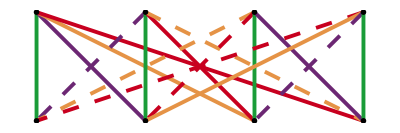

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | -1 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | -1 | 0 | 0),(0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)}

```mathematica
GraphAdinkra[Q]
PrintAllL[Q]
```

```mathematica
LocalRep = -111751;
```

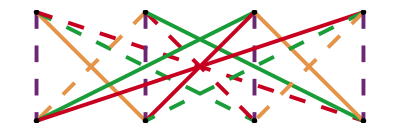

{(0 | 0 | 1 | 0
0 | 0 | 0 | -1
-1 | 0 | 0 | 0
0 | 1 | 0 | 0),(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1),(0 | -1 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | 1 | 0),(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | -1 | 0 | 0
-1 | 0 | 0 | 0)}

```mathematica
GraphAdinkra[LocalRep]
PrintAllL[LocalRep]
```

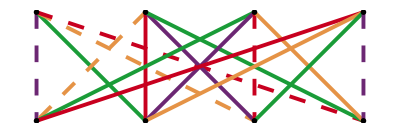

{(0 | 0 | 1 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0),(-1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | -1),(0 | -1 | 0 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | 0 | 1 | 0),(0 | 0 | 0 | 1
0 | 1 | 0 | 0
0 | 0 | -1 | 0
-1 | 0 | 0 | 0)}

```mathematica
LocalRep = -441751;
GraphAdinkra[LocalRep]
PrintAllL[LocalRep]
Clear[LocalRep]
```

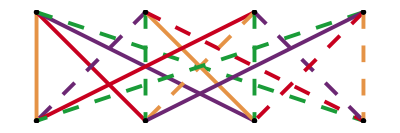

{(0 | 0 | 0 | -1
0 | -1 | 0 | 0
0 | 0 | -1 | 0
-1 | 0 | 0 | 0),(0 | -1 | 0 | 0
0 | 0 | 0 | 1
1 | 0 | 0 | 0
0 | 0 | -1 | 0),(1 | 0 | 0 | 0
0 | 0 | -1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | -1),(0 | 0 | 1 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | -1 | 0 | 0)}

```mathematica
LocalRep = -442751;
GraphAdinkra[LocalRep]
PrintAllL[LocalRep]
Clear[LocalRep]
```

### Raising Operator: RaiseOpM4[m,word]

```mathematica
RaiseOpM4[m_,word_]:=({{m^(IntegerDigits[word,2,4][[4]]), 0, 0, 0}, {0, m^(IntegerDigits[word,2,4][[3]]), 0, 0}, {0, 0, m^(IntegerDigits[word,2,4][[2]]), 0}, {0, 0, 0, m^(IntegerDigits[word,2,4][[1]])}})
```

```mathematica
Table[RaiseOpM4[m,wordnum]//MatrixForm,{wordnum,0,15}]
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(m | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | m | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(m | 0 | 0 | 0
0 | m | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | m | 0
0 | 0 | 0 | 1),(m | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | m | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | m | 0 | 0
0 | 0 | m | 0
0 | 0 | 0 | 1),(m | 0 | 0 | 0
0 | m | 0 | 0
0 | 0 | m | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | m),(m | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | m),(1 | 0 | 0 | 0
0 | m | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | m),(m | 0 | 0 | 0
0 | m | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | m),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | m | 0
0 | 0 | 0 | m),(m | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | m | 0
0 | 0 | 0 | m),(1 | 0 | 0 | 0
0 | m | 0 | 0
0 | 0 | m | 0
0 | 0 | 0 | m),(m | 0 | 0 | 0
0 | m | 0 | 0
0 | 0 | m | 0
0 | 0 | 0 | m)}

```mathematica
LRaised4[Rep_][m_,word_]:=Table[ RaiseOpM4[m,word].L[Rep][[II]],{II,1,4}]
RRaised4[Rep_][mu_,word_] :=Table[ Transpose[L[Rep][[II]]].Inverse[RaiseOpM4[mu,word]],{II,1,4}]
```

#### Test on the Rep = -864861

```mathematica
LocalRep = -864861;
```

```mathematica
RRaised4[LocalRep][m/ρ,1][[2]]
```

{{-ρ/m,0,0,0},{0,0,1,0},{0,0,0,-1},{0,-1,0,0}}

```mathematica
LRaised4[LocalRep][m,1][[2]]//MatrixForm
```

(-m | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 1 | 0 | 0
0 | 0 | -1 | 0)

```mathematica
GATest[LRaised4[LocalRep][m,3],RRaised4[LocalRep][m,3]]
```

True

```mathematica
GATest[LRaised4[LocalRep][m,3],RRaised4[LocalRep][m/ρ,3]]/.ρ-> 1
```

True

```mathematica
Clear[LocalRep]
```

### BL = L4.R3.L2.R1 and BR = R4.L3.R2.L1

```mathematica
B[L][Rep_][word_]:= LRaised4[Rep][m,word][[4]].RRaised4[Rep][m/ρ,word][[3]].LRaised4[Rep][m,word][[2]].RRaised4[Rep][m/ρ,word][[1]]
B[R][Rep_][word_]:= RRaised4[Rep][m/ρ,word][[4]].LRaised4[Rep][m,word][[3]].RRaised4[Rep][m/ρ,word][[2]].LRaised4[Rep][m,word][[1]]
```

```mathematica
χ0[Rep_] :=CalculateChi0[L[Rep],RO[Rep]] (* Calculation of chi0 without need of generating R matrices, assumes orthogonal adinkra matrices L = R^T*)
```

```mathematica
GR44RepList = Table[(-1)^p1*(aa*10^5+mu*10^4+AA*10^3+bb*10^2+nu*10^1+tt),{p1,0,1},{aa,1,8},{mu,1,6},{AA,1,4},{bb,1,8},{nu,1,6},{tt,1,2}]//Flatten;  (* List of all Rep Codes for the GR44 valise adinkras as in *)
```

```mathematica
Dimensions[GR44RepList]
```

{36864}

```mathematica
B[L][-111111][1]
```

{{-ρ,0,0,0},{0,-ρ,0,0},{0,0,-1,0},{0,0,0,-1}}

```mathematica
χ0[-111111]
```

-1

```mathematica
RepNo = 5891
χ0[GR44RepList[[RepNo]]]Eigenvalues[B[R][GR44RepList[[RepNo]]][15]]
Clear[RepNo]
```

5891

{-ρ^2,-ρ^2,-ρ^2,-ρ^2}

### zero nodes raised: w = 0 Prints True/False whether the eigenvalues of B_L are correct or not and True/False whether the eigenvalues of B_R are correct or not

```mathematica
LocalNumReps = 100;
LocalRandomRepList =RandomInteger[{1,36864},LocalNumReps];
LocalWord = 0; (*Valise *)
BEigens[L][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{1,1,1,1},{RepNo,LocalRandomRepList}];
BEigens[R][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{-1,-1,-1,-1},{RepNo,LocalRandomRepList}];BEigens[L][LocalWord,4,4]==Table[Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
BEigens[R][LocalWord,4,4]==Table[Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
Print[StringJoin["Word = ", ToString[LocalWord]]]
Print[StringJoin["Reps Randomly Checked  are ", ToString[LocalRandomRepList]]]
Clear[LocalWord,LocalRandomRepList,LocalNumReps]
```

True

True

Word = 0

Reps Randomly Checked  are {1217, 16063, 12038, 20728, 35894, 13936, 2991, 27991, 23310, 17193, 8779, 18185, 25574, 11080, 31218, 26656, 26643, 18685, 33002, 26914, 20309, 9566, 22092, 25272, 15824, 5755, 20335, 6055, 19657, 11552, 36221, 23272, 16392, 35581, 17684, 34958, 15407, 9678, 5592, 34223, 27987, 10238, 33989, 27840, 18558, 9082, 9752, 175, 4980, 7861, 35776, 9138, 20112, 17685, 27164, 30093, 32063, 7133, 15719, 18470, 15201, 29712, 29840, 34293, 16741, 24220, 22499, 13780, 7371, 24409, 19625, 22546, 25384, 4303, 26659, 33747, 14009, 7244, 16779, 8939, 36333, 17112, 17649, 1281, 19552, 2039, 31036, 20097, 27126, 21233, 27023, 3837, 20599, 34423, 31517, 22460, 27328, 17617, 16560, 2771}

### One Nodes Raised: w = 1,2,4,8 Prints True/False whether the eigenvalues of B_L are correct or not and True/False whether the eigenvalues of B_R are correct or not

#### one node raised: w = 1

```mathematica
LocalNumReps = 100;
LocalRandomRepList =RandomInteger[{1,36864},LocalNumReps];
LocalWord = 1; (* First node raised *)
BEigens[L][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{1,1,ρ,ρ},{RepNo,LocalRandomRepList}];
BEigens[R][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{-1,-1,-ρ,-ρ},{RepNo,LocalRandomRepList}];BEigens[L][LocalWord,4,4]==Table[Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
BEigens[R][LocalWord,4,4]==Table[Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
Print[StringJoin["Word = ", ToString[LocalWord]]]
Print[StringJoin["Reps Randomly Checked  are ", ToString[LocalRandomRepList]]]
Clear[LocalWord,LocalRandomRepList,LocalNumReps]
```

True

True

Word = 1

Reps Randomly Checked  are {17222, 26935, 3534, 25431, 19520, 11554, 3810, 27591, 20712, 23221, 26307, 35537, 20246, 9068, 24396, 14656, 19926, 21919, 22805, 5056, 3922, 31260, 31394, 35585, 26858, 4147, 27217, 2785, 12633, 7125, 18274, 33128, 13647, 22967, 22572, 13185, 211, 5819, 5685, 13089, 34151, 5728, 7838, 28005, 4912, 19881, 24523, 29474, 27769, 12922, 9707, 31595, 30645, 31964, 27817, 24788, 9452, 33858, 7972, 35595, 5472, 10370, 34699, 34063, 28176, 14788, 12196, 30601, 1444, 30498, 30876, 1142, 9318, 20624, 31785, 18773, 3459, 14466, 36249, 27477, 15131, 9137, 17879, 18762, 30666, 34162, 22056, 1791, 18802, 28612, 12793, 2636, 11707, 27358, 16599, 26218, 35663, 2699, 13108, 27025}

#### one node raised: w = 2

```mathematica
LocalNumReps = 100;
LocalRandomRepList =RandomInteger[{1,36864},LocalNumReps];
LocalWord = 2; 
BEigens[L][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{1,1,ρ,ρ},{RepNo,LocalRandomRepList}];
BEigens[R][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{-1,-1,-ρ,-ρ},{RepNo,LocalRandomRepList}];BEigens[L][LocalWord,4,4]==Table[Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
BEigens[R][LocalWord,4,4]==Table[Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
Print[StringJoin["Word = ", ToString[LocalWord]]]
Print[StringJoin["Reps Randomly Checked  are ", ToString[LocalRandomRepList]]]
Clear[LocalWord,LocalRandomRepList,LocalNumReps]
```

True

True

Word = 2

Reps Randomly Checked  are {4700, 23744, 19340, 5727, 30460, 28739, 5756, 36307, 34868, 33079, 4644, 17898, 20570, 3624, 16654, 25941, 30327, 26520, 3178, 31397, 7827, 14774, 7909, 21161, 32406, 33557, 32735, 22019, 18012, 4318, 3730, 14944, 29472, 3203, 20438, 34063, 4648, 175, 34183, 20488, 17067, 21955, 13093, 36520, 22953, 13924, 30447, 20798, 407, 10819, 6376, 31371, 31909, 23439, 1349, 13905, 4220, 11037, 30106, 21704, 7392, 17211, 19195, 30634, 11739, 20358, 13557, 22686, 25054, 29427, 29544, 2994, 5590, 14813, 26646, 12731, 24229, 9985, 5412, 33137, 33198, 14086, 18244, 21559, 14179, 33763, 10168, 9148, 11645, 20515, 22293, 23112, 26151, 1273, 24824, 10128, 36591, 14808, 33060, 14320}

#### one node raised: w = 4

```mathematica
LocalNumReps = 100;
LocalRandomRepList =RandomInteger[{1,36864},LocalNumReps];
LocalWord = 4; 
BEigens[L][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{1,1,ρ,ρ},{RepNo,LocalRandomRepList}];
BEigens[R][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{-1,-1,-ρ,-ρ},{RepNo,LocalRandomRepList}];BEigens[L][LocalWord,4,4]==Table[Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
BEigens[R][LocalWord,4,4]==Table[Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
Print[StringJoin["Word = ", ToString[LocalWord]]]
Print[StringJoin["Reps Randomly Checked  are ", ToString[LocalRandomRepList]]]
Clear[LocalWord,LocalRandomRepList,LocalNumReps]
```

True

True

Word = 4

Reps Randomly Checked  are {29872, 22039, 2399, 13752, 13707, 32484, 3130, 1319, 6490, 8902, 29830, 28696, 14955, 7493, 10841, 6458, 26710, 18829, 6657, 30865, 26006, 16426, 18525, 4538, 19749, 23325, 34287, 25543, 26549, 1178, 35334, 23448, 3421, 7729, 864, 30397, 7167, 18897, 32714, 575, 24616, 29707, 36290, 15291, 30766, 4986, 23729, 20213, 26582, 1432, 22899, 31904, 22413, 7579, 12115, 18727, 8486, 3340, 19039, 12363, 22176, 35933, 11728, 4532, 34298, 32743, 8781, 18493, 12805, 10006, 25077, 26811, 30295, 24577, 1641, 419, 8610, 31868, 5215, 20114, 13233, 18689, 24173, 28982, 8774, 29548, 23601, 29649, 904, 4962, 36672, 860, 10884, 14453, 28322, 1020, 12483, 27625, 31089, 4036}

#### one node raised: w = 8

```mathematica
LocalNumReps = 100;
LocalRandomRepList =RandomInteger[{1,36864},LocalNumReps];
LocalWord = 8; 
BEigens[L][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{1,1,ρ,ρ},{RepNo,LocalRandomRepList}];
BEigens[R][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{-1,-1,-ρ,-ρ},{RepNo,LocalRandomRepList}];BEigens[L][LocalWord,4,4]==Table[Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
BEigens[R][LocalWord,4,4]==Table[Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
Print[StringJoin["Word = ", ToString[LocalWord]]]
Print[StringJoin["Reps Randomly Checked  are ", ToString[LocalRandomRepList]]]
Clear[LocalWord,LocalRandomRepList,LocalNumReps]
```

True

True

Word = 8

Reps Randomly Checked  are {2655, 32241, 11525, 30794, 9913, 12569, 178, 24918, 2821, 10842, 22446, 11840, 14317, 14782, 36633, 5936, 32647, 35854, 24808, 28217, 1826, 6968, 22333, 14860, 27510, 22524, 4612, 4635, 18091, 1044, 19054, 5833, 14481, 6107, 5074, 6844, 26632, 31871, 14029, 32362, 23967, 30459, 21409, 12329, 2401, 335, 1346, 28744, 6367, 35941, 23264, 17224, 32319, 12561, 30109, 36017, 20819, 32699, 2444, 18711, 12620, 12736, 5293, 53, 36862, 24905, 25562, 741, 2346, 28624, 4610, 32130, 30003, 17181, 8, 13077, 15300, 15588, 35155, 27058, 30475, 5235, 22491, 15189, 4657, 21469, 15391, 32964, 19758, 15044, 8931, 19993, 12380, 24131, 32613, 31228, 33753, 29001, 18832, 20660}

### Two Nodes Raised, (w,15-w) = (3,12),(5,10),(6,9) Prints a singleTrue/False if the Eigenvalue Equivalence Classes are paired as (w,15-w) or not and if they fall into one of the three Eigenvalue Equivalence classes for B_L and B_R or not

```mathematica
BEigensPair[1][L][Rep_]:= χ0[Rep]*{ρ,ρ,ρ,ρ}
BEigensPair[1][R][Rep_]:= χ0[Rep]*{-1,-1,-ρ^2,-ρ^2}
BEigensPair[2][L][Rep_]:= χ0[Rep]*{1,1,ρ^2,ρ^2}
BEigensPair[2][R][Rep_]:= χ0[Rep]*{-ρ,-ρ,-ρ,-ρ}
BEigensPair[3][L][Rep_]:= χ0[Rep]*{ρ,ρ,ρ,ρ}
BEigensPair[3][R][Rep_]:= χ0[Rep]*{-ρ,-ρ,-ρ,-ρ}
```

#### two nodes raised: (w,15-w) = (3,12)

```mathematica
LocalNumReps = 100;
LocalRandomRepList =RandomInteger[{1,36864},LocalNumReps];
LocalWord = 3; 
Table[Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]]==Eigenvalues[B[L][GR44RepList[[RepNo]]][15-LocalWord]]&&Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]]==Eigenvalues[B[R][GR44RepList[[RepNo]]][15-LocalWord]]&&((Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]]==BEigensPair[1][L][GR44RepList[[RepNo]]]&&Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]]==BEigensPair[1][R][GR44RepList[[RepNo]]])||(Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]]==BEigensPair[2][L][GR44RepList[[RepNo]]]&&Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]]==BEigensPair[2][R][GR44RepList[[RepNo]]])||(Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]]==BEigensPair[3][L][GR44RepList[[RepNo]]]&&Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]]==BEigensPair[3][R][GR44RepList[[RepNo]]])),{RepNo,LocalRandomRepList}]==Table[True,{RepNo,LocalRandomRepList}]
Print[StringJoin["Equivalence Word Pair = (", ToString[LocalWord]], ", ", ToString[15-LocalWord], ")"]
Print[StringJoin["Reps Randomly Checked  are ", ToString[LocalRandomRepList]]]
Clear[LocalWord,LocalRandomRepList,LocalNumReps]
```

True

Equivalence Word Pair = (3, 12)

Reps Randomly Checked  are {29593, 17307, 23199, 33751, 28349, 14320, 9349, 9692, 7510, 2484, 6220, 8410, 20571, 11348, 15794, 28422, 16793, 33662, 12884, 12608, 21720, 4868, 1739, 14018, 9774, 24922, 29431, 13700, 15149, 612, 16217, 20475, 31821, 5278, 7913, 30617, 1436, 27134, 28948, 35, 17244, 8376, 26559, 31702, 18705, 8674, 24378, 15075, 11476, 11958, 8629, 6815, 22014, 21728, 21484, 20286, 2832, 20261, 14701, 29360, 2264, 36762, 30460, 13466, 1978, 19038, 1342, 24212, 3526, 25219, 31246, 23395, 5666, 1389, 10798, 32888, 19277, 24761, 10446, 28663, 31357, 32384, 35845, 17039, 11165, 24172, 4142, 30582, 14878, 26821, 15690, 1003, 18175, 17021, 29214, 29099, 22284, 15985, 16221, 16371}

#### two nodes raised: (w,15-w) = (5,10)

```mathematica
LocalNumReps = 100;
LocalRandomRepList =RandomInteger[{1,36864},LocalNumReps];
LocalWord = 5; 
Table[Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]]==Eigenvalues[B[L][GR44RepList[[RepNo]]][15-LocalWord]]&&Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]]==Eigenvalues[B[R][GR44RepList[[RepNo]]][15-LocalWord]]&&((Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]]==BEigensPair[1][L][GR44RepList[[RepNo]]]&&Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]]==BEigensPair[1][R][GR44RepList[[RepNo]]])||(Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]]==BEigensPair[2][L][GR44RepList[[RepNo]]]&&Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]]==BEigensPair[2][R][GR44RepList[[RepNo]]])||(Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]]==BEigensPair[3][L][GR44RepList[[RepNo]]]&&Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]]==BEigensPair[3][R][GR44RepList[[RepNo]]])),{RepNo,LocalRandomRepList}]==Table[True,{RepNo,LocalRandomRepList}]
Print[StringJoin["Equivalence Word Pair = (", ToString[LocalWord]], ", ", ToString[15-LocalWord], ")"]
Print[StringJoin["Reps Randomly Checked  are ", ToString[LocalRandomRepList]]]
Clear[LocalWord,LocalRandomRepList,LocalNumReps]
```

True

Equivalence Word Pair = (5, 10)

Reps Randomly Checked  are {649, 18123, 33342, 25259, 6800, 2306, 17668, 11139, 11580, 13567, 7999, 1508, 13948, 34486, 1372, 18020, 13975, 28754, 26520, 5540, 30135, 16687, 3366, 30757, 12310, 11220, 21532, 25176, 558, 4234, 13290, 3388, 19364, 26577, 3124, 24525, 34915, 1986, 26931, 27373, 14276, 21302, 12786, 2093, 27052, 23376, 36154, 28178, 34297, 24031, 25059, 28393, 24752, 5911, 9510, 14063, 17651, 34913, 2816, 6772, 26440, 28300, 32287, 12059, 8388, 1709, 29743, 25079, 18134, 17532, 23108, 29930, 15414, 13760, 32323, 36186, 34798, 31328, 28285, 30169, 9507, 15063, 18520, 7732, 17516, 23446, 18394, 13630, 33498, 15163, 1377, 16008, 6991, 12414, 35647, 7167, 11152, 7538, 16085, 7665}

#### two nodes raised: (w,15-w) = (6,9)

```mathematica
LocalNumReps = 100;
LocalRandomRepList =RandomInteger[{1,36864},LocalNumReps];
LocalWord = 6; 
Table[Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]]==Eigenvalues[B[L][GR44RepList[[RepNo]]][15-LocalWord]]&&Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]]==Eigenvalues[B[R][GR44RepList[[RepNo]]][15-LocalWord]]&&((Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]]==BEigensPair[1][L][GR44RepList[[RepNo]]]&&Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]]==BEigensPair[1][R][GR44RepList[[RepNo]]])||(Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]]==BEigensPair[2][L][GR44RepList[[RepNo]]]&&Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]]==BEigensPair[2][R][GR44RepList[[RepNo]]])||(Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]]==BEigensPair[3][L][GR44RepList[[RepNo]]]&&Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]]==BEigensPair[3][R][GR44RepList[[RepNo]]])),{RepNo,LocalRandomRepList}]==Table[True,{RepNo,LocalRandomRepList}]
Print[StringJoin["Equivalence Word Pair = (", ToString[LocalWord]], ", ", ToString[15-LocalWord], ")"]
Print[StringJoin["Reps Randomly Checked  are ", ToString[LocalRandomRepList]]]
Clear[LocalWord,LocalRandomRepList,LocalNumReps]
```

True

Equivalence Word Pair = (6, 9)

Reps Randomly Checked  are {1625, 8772, 17363, 18489, 23998, 18777, 16812, 19583, 34229, 34249, 1177, 29829, 24890, 8273, 8107, 12525, 30587, 457, 7460, 32698, 35300, 15637, 8656, 917, 2436, 16944, 17550, 23880, 9603, 1540, 29286, 17566, 13976, 17150, 14447, 27113, 13189, 20740, 29509, 4783, 10166, 14738, 31331, 16963, 24397, 21998, 16798, 2114, 218, 7128, 32158, 7450, 14735, 26535, 18305, 15089, 5236, 22461, 2948, 25942, 11960, 22201, 32293, 27515, 5061, 2650, 32131, 26647, 10843, 15765, 11953, 1330, 23165, 8982, 15701, 12947, 6922, 31134, 30734, 27812, 23912, 11123, 500, 18006, 25560, 33965, 17542, 16369, 25642, 27158, 388, 21038, 13461, 4871, 27864, 26946, 7101, 5991, 22970, 9512}

### three nodes raised: w = 7,11,13,14 Prints True/False whether the eigenvalues of B_L are correct or not and True/False whether the eigenvalues of B_R are correct or not

#### three nodes raised: w = 7

```mathematica
LocalNumReps = 100;
LocalRandomRepList =RandomInteger[{1,36864},LocalNumReps];
LocalWord = 7; 
BEigens[L][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{ρ,ρ,ρ^2,ρ^2},{RepNo,LocalRandomRepList}];
BEigens[R][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{-ρ,-ρ,-ρ^2,-ρ^2},{RepNo,LocalRandomRepList}];BEigens[L][LocalWord,4,4]==Table[Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
BEigens[R][LocalWord,4,4]==Table[Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
Print[StringJoin["Word = ", ToString[LocalWord]]]
Print[StringJoin["Reps Randomly Checked  are ", ToString[LocalRandomRepList]]]
Clear[LocalWord,LocalRandomRepList,LocalNumReps]
```

True

True

Word = 7

Reps Randomly Checked  are {29755, 24181, 22519, 32510, 6457, 15350, 28860, 3891, 34286, 33806, 23792, 22976, 30580, 31894, 30308, 10673, 1537, 31333, 26167, 35176, 33999, 15117, 775, 30447, 24771, 30929, 13146, 29307, 5741, 16636, 648, 17727, 17583, 15620, 21610, 25379, 17776, 4615, 19317, 34416, 2767, 27440, 14735, 2785, 13907, 25439, 13018, 3974, 18427, 31366, 12176, 21464, 5106, 14257, 3470, 19538, 26465, 18193, 14206, 17241, 29032, 26807, 32953, 31378, 3131, 28539, 2785, 10726, 25204, 9450, 3080, 30659, 9914, 34089, 8589, 21987, 32364, 35606, 18924, 29184, 8605, 15619, 15215, 17726, 34042, 20770, 24849, 33487, 35791, 12648, 471, 2936, 21574, 27420, 6762, 18211, 734, 33566, 7683, 11935}

#### three nodes raised: w = 11

```mathematica
LocalNumReps = 100;
LocalRandomRepList =RandomInteger[{1,36864},LocalNumReps];
LocalWord =11; 
BEigens[L][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{ρ,ρ,ρ^2,ρ^2},{RepNo,LocalRandomRepList}];
BEigens[R][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{-ρ,-ρ,-ρ^2,-ρ^2},{RepNo,LocalRandomRepList}];BEigens[L][LocalWord,4,4]==Table[Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
BEigens[R][LocalWord,4,4]==Table[Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
Print[StringJoin["Word = ", ToString[LocalWord]]]
Print[StringJoin["Reps Randomly Checked  are ", ToString[LocalRandomRepList]]]
Clear[LocalWord,LocalRandomRepList,LocalNumReps]
```

True

True

Word = 11

Reps Randomly Checked  are {3376, 16573, 14473, 2815, 19889, 11628, 8599, 20278, 14077, 8958, 10330, 30190, 17391, 8255, 30034, 16649, 35896, 20501, 36799, 13646, 12266, 19661, 22957, 27172, 31909, 11345, 18479, 10052, 13339, 18379, 35912, 35943, 5145, 34741, 20637, 23184, 23209, 17677, 22761, 14675, 2997, 29386, 10275, 32202, 26341, 27605, 23047, 16791, 27921, 34450, 31425, 34108, 7703, 5789, 15353, 14656, 30040, 8333, 23734, 18274, 7716, 16547, 30898, 23171, 3192, 14820, 31408, 20235, 28554, 8910, 19367, 27794, 20262, 33468, 1611, 21951, 19292, 25850, 35691, 6364, 32353, 28319, 22171, 15272, 21073, 27622, 25399, 18782, 15250, 1477, 10715, 17656, 14546, 29255, 33021, 34930, 28164, 3275, 18944, 13351}

#### three nodes raised: w = 13

```mathematica
LocalNumReps = 100;
LocalRandomRepList =RandomInteger[{1,36864},LocalNumReps];
LocalWord =13; 
BEigens[L][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{ρ,ρ,ρ^2,ρ^2},{RepNo,LocalRandomRepList}];
BEigens[R][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{-ρ,-ρ,-ρ^2,-ρ^2},{RepNo,LocalRandomRepList}];BEigens[L][LocalWord,4,4]==Table[Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
BEigens[R][LocalWord,4,4]==Table[Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
Print[StringJoin["Word = ", ToString[LocalWord]]]
Print[StringJoin["Reps Randomly Checked  are ", ToString[LocalRandomRepList]]]
Clear[LocalWord,LocalRandomRepList,LocalNumReps]
```

True

True

Word = 13

Reps Randomly Checked  are {6914, 21861, 3106, 32124, 26215, 31569, 16771, 24194, 12358, 26281, 19254, 707, 6516, 21228, 4874, 626, 5803, 24297, 24687, 35401, 6145, 29552, 23008, 34951, 16763, 15168, 21885, 5981, 23386, 20185, 20677, 288, 23177, 2459, 15578, 7321, 11634, 12053, 29132, 9113, 1463, 12513, 791, 30434, 21032, 21193, 20344, 10388, 28721, 4397, 26600, 21886, 23250, 8248, 1344, 30679, 21046, 8549, 28119, 20776, 28899, 23717, 35939, 5852, 3310, 32677, 11332, 17274, 9624, 14692, 20367, 31501, 18990, 35034, 36021, 3280, 17348, 10949, 12063, 26465, 24629, 16363, 736, 30877, 35795, 20017, 5172, 3494, 9932, 33656, 32509, 7185, 419, 14891, 12432, 6301, 14845, 27644, 22045, 15565}

#### three nodes raised: w = 14

```mathematica
LocalNumReps = 100;
LocalRandomRepList =RandomInteger[{1,36864},LocalNumReps];
LocalWord =14; 
BEigens[L][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{ρ,ρ,ρ^2,ρ^2},{RepNo,LocalRandomRepList}];
BEigens[R][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{-ρ,-ρ,-ρ^2,-ρ^2},{RepNo,LocalRandomRepList}];BEigens[L][LocalWord,4,4]==Table[Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
BEigens[R][LocalWord,4,4]==Table[Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
Print[StringJoin["Word = ", ToString[LocalWord]]]
Print[StringJoin["Reps Randomly Checked  are ", ToString[LocalRandomRepList]]]
Clear[LocalWord,LocalRandomRepList,LocalNumReps]
```

True

True

Word = 14

Reps Randomly Checked  are {741, 3204, 1154, 24289, 6475, 19662, 12615, 11578, 17887, 5792, 10554, 27286, 35432, 25554, 21337, 33889, 30895, 3557, 27627, 21846, 1626, 10547, 4859, 15653, 12765, 16047, 35599, 5586, 27818, 29268, 16314, 13928, 9351, 13166, 10860, 8296, 4733, 13451, 10375, 32781, 5622, 9033, 17007, 777, 8940, 26986, 6034, 30319, 27673, 4597, 16448, 11190, 28443, 23173, 26478, 13050, 20520, 32954, 14030, 33917, 29742, 20322, 5362, 8957, 3143, 28544, 4894, 30286, 35786, 21514, 3008, 23595, 12032, 1245, 5573, 13254, 31637, 11097, 31060, 6876, 13118, 22980, 11291, 23378, 15280, 30122, 16581, 2552, 5454, 35431, 2244, 32272, 13381, 7656, 16438, 4940, 16552, 21784, 14440, 23185}

### all four nodes raised: w = 15 Prints True/False whether the eigenvalues of B_L are correct or not and True/False whether the eigenvalues of B_R are correct or not

```mathematica
LocalNumReps = 100;
LocalRandomRepList =RandomInteger[{1,36864},LocalNumReps];
LocalWord =15; 
BEigens[L][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{ρ^2,ρ^2,ρ^2,ρ^2},{RepNo,LocalRandomRepList}];
BEigens[R][LocalWord,4,4] =Table[χ0[GR44RepList[[RepNo]]]*{-ρ^2,-ρ^2,-ρ^2,-ρ^2},{RepNo,LocalRandomRepList}];BEigens[L][LocalWord,4,4]==Table[Eigenvalues[B[L][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
BEigens[R][LocalWord,4,4]==Table[Eigenvalues[B[R][GR44RepList[[RepNo]]][LocalWord]],{RepNo,LocalRandomRepList}]
Print[StringJoin["Word = ", ToString[LocalWord]]]
Print[StringJoin["Reps Randomly Checked  are ", ToString[LocalRandomRepList]]]
Clear[LocalWord,LocalRandomRepList,LocalNumReps]
```

True

True

Word = 15

Reps Randomly Checked  are {31926, 24920, 2055, 29716, 3724, 12017, 12331, 18136, 3966, 32242, 9938, 28417, 29971, 30024, 15851, 9192, 9863, 33532, 10162, 27042, 19399, 10348, 12973, 21312, 5893, 24242, 34684, 11016, 10917, 14421, 34363, 5611, 32037, 28841, 36334, 4311, 13785, 13352, 26452, 33468, 29838, 13153, 27916, 26738, 5002, 14808, 20055, 27083, 35865, 15429, 2592, 24229, 2790, 1075, 2550, 11914, 14482, 36273, 25093, 25128, 15992, 17463, 6787, 3343, 25209, 26750, 15026, 36645, 34796, 24975, 12951, 26179, 23904, 12706, 26472, 25014, 28433, 8731, 36273, 12942, 6482, 18925, 17695, 6175, 27754, 17682, 33360, 14037, 35448, 30441, 24543, 29735, 13567, 12543, 26846, 16145, 26584, 19883, 11950, 2897}